```mathematica
ClearAll[guess];
guess[n1_,n2_] := Sum[(2k+2l)!/k!^2/l!^2z1^k z2^l, {k, 0, n1}, {l, 0, n2}];
guess[Infinity,Infinity]
%/.{z1->1/U^2, z2->R^4/U^2}//PowerExpand
```

∑_(k=0)^∞ ∑_(l=0)^∞ (z1^k z2^l (2 k+2 l)!)/((k!)^2 (l!)^2)

∑_(k=0)^∞ ∑_(l=0)^∞ (R^(4 l) U^(-2 k-2 l) (2 k+2 l)!)/((k!)^2 (l!)^2)

```mathematica
With[{k=2,l=3},(2k+2l)!/k!/l!-D[AppellF4[1/2,1,1,1,4z1,4z2], {z1,k}, {z2,l}]/.{z1->0,z2->0}]
```

0

```mathematica
D[AppellF4[1/2,1,1,1,4z1,4z2], {z1,k}, {z2,l}]/.{z1->0,z2->0}//FullSimplify
```

Gamma[1+2 k+2 l]/(Gamma[1+k] Pochhammer[1,l])

```mathematica
FullSimplify[AppellF4[1/2,1,1,1,4z1,4z2], {Im[z1]>0, Im[z2]>0}]
```

AppellF4[1/2,1,1,1,4 z1,4 z2]

```mathematica
Gamma[1]
```

1

```mathematica
Gamma[5+1]==5!
```

True

## Richardson

```mathematica
a1[lam_, n_]:=Sum[(2n)!/(n-l)!^2/l!^2 lam^l, {l, 0, n}];
```

```mathematica
a2[lam_, n_]:=Sum[(2n-1)!/(n-l)!^2/l!^2 lam^l, {l, 0, n}];
```

```mathematica
Table[a2[1, n](1/16)^n, {n, 1, 1000}];
sums = N[Log[1/16]+2Accumulate[%], 200];
```

```mathematica
(Last[sums]/(2Pi I))-(4 I Catalan/Pi^2)//Im
```

0.00005062894425114080653681812239063172565469260101487800444306770834118186882001827685098188719935190881630207088052573742973434109835911411338341722932534914687028884127917330683668541783962108871855

```mathematica
sums//Length
```

1000

```mathematica
With[{M = 20},
Table[Sum[sums[[n+l]](n+l)^M(-1)^(l+M)/(Factorial[l]Factorial[M-l]), {l, 0, M}], {n, 1, Length[sums]-M}]
];
N[{4 I Catalan/Pi^2, Last[sums]/(2Pi I), %/(2Pi I)}, 100]
```

{0.371226872710772162953963980399439971218860918262586410815203838782252242575155503583455425509247272 ⅈ,0.3712775016550233037605007985218306029445156108636012888196469064905934244439755218603064073964466239 ⅈ,0.3712268727107721629539639803994399712188609182625864108152037082423518360707609878395904957208579032 ⅈ}

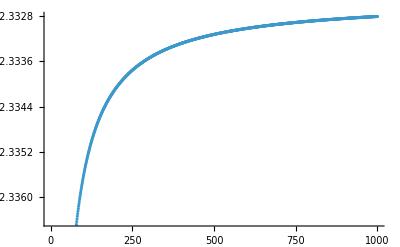

```mathematica
ListPlot[sums]
```

```mathematica
Log[z]+2(a2[lam,1]z+a2[lam,2]z^2+a2[lam,3]z^3+a2[lam,4]z^4)
Series[%, {z, 0, 10}]
```

2 ((1+lam) z+(3/2+6 lam+(3 lam^2)/2) z^2+(10/3+30 lam+30 lam^2+(10 lam^3)/3) z^3+(35/4+140 lam+315 lam^2+140 lam^3+(35 lam^4)/4) z^4)+Log[z]

Log[z]+2 (1+lam) z+3 (1+4 lam+lam^2) z^2+20/3 (1+9 lam+9 lam^2+lam^3) z^3+35/2 (1+16 lam+36 lam^2+16 lam^3+lam^4) z^4+O[z]^11

```mathematica
With[{d=5},
eqn = Flatten[{Sum[A[i], {i, d}]==1, Table[Sum[A[i]/2^((i-1)(p+k)), {i, d}]==0, {k, 0, d-2}]}];
Solve[eqn, Array[A, d]]//Expand//Simplify
]
```

{{A[1]→1/((-1+2^p) (-1+2^(1+p)) (1-3 2^(2+p)+2^(5+2 p))),A[2]→-(15 2^p)/((-1+2^p) (-1+2^(3+p)) (1-3 2^(1+p)+2^(3+2 p))),A[3]→(35 2^(1+2 p))/((-1+2^p) (-1+2^(1+p)) (-1+2^(2+p)) (-1+2^(3+p))),A[4]→-(15 8^(1+p))/((-1+2^p) (-1+2^(1+p)) (-1+2^(2+p)) (-1+2^(3+p))),A[5]→4^(3+2 p)/((-1+2^p) (-1+2^(1+p)) (-1+2^(2+p)) (-1+2^(3+p)))}}

```mathematica
{(-1)^(d-1), Sum[(-1)^j(Nn+j)^(p+d-2)/j!/(d-1-j)!, {j, 0, d-1}]/.{p->1}}/.{Nn->10213, d->6}
```

{-1,-1}

```mathematica
RichardsonA[sums_, Nn_, p_]:=Module[{d},
d = Length[sums];
Sum[(-1)^i(Nn+i)^(p+d-2)/i!/(d-1-i)! sums[[i+1]], {i, 0, d-1}]/Sum[(-1)^j(Nn+j)^(p+d-2)/j!/(d-1-j)!, {j, 0, d-1}]
];
```

```mathematica
RichardsonA[sums_, Nn_, 1]:=With[{d=Length[sums]},
Sum[(-1)^(i+d-1)N[(Nn+i)^(d-1)/i!/(d-1-i)! , 300]*sums[[i+1]], {i, 0, d-1}]
];
```

```mathematica
Table[(-1)^(k+1)/k, {k, 1, 1999}];
Sums = Accumulate[%];
With[{d=10,p=1},
sums = N[Take[Sums, -d], 100];
r=RichardsonA[sums, Echo[Length[Sums]-d+1], p];
N[{Log[2], Last[Sums], r}, 100]
]
```

1990

{0.6931471805599453094172321214581765680755001343602552541206800094933936219696947156058633269964186875,0.6933972430599374969211383673077935114137875712036840744467825132437212089745819478346931174614662828,1.76622996801824363824585516642579957551185563894197149817559011528294982664646532964740775332185×10^23}

```mathematica
Table[(-1)^(k+1)/k, {k, 1, 500}];
sums = Accumulate[%];
Print[Length[sums]];

With[{Nn=490, p=1},
Print["d=",Length[sums]-Nn+1];
subs = With[{d=Length[sums]-Nn+1},
Table[alp[i]->
(-1)^i(Nn+i)^(p+d-2)/i!/(d-1-i)!/Sum[(-1)^j (Nn+j)^(p+d-2)/j!/(d-1-j)!, {j, 0, d-1}]
, {i,0,d-1}]
];
Print[N[subs]];
(*Print[N[Table[sums[[Nn+i]], {i, 0, Length[sums]-Nn}], 100]];*)
N[{Log[2], Last[sums],Sum[alp[i]*sums[[Nn+i]], {i, 0, Length[sums]-Nn}]/.subs}, 100]
]
```

500

d=11

{alp[0.]→2.19886×10^20,alp[1.]→-2.24415×10^21,alp[2.]→1.03062×10^22,alp[3.]→-2.80471×10^22,alp[4.]→5.00871×10^22,alp[5.]→-6.13323×10^22,alp[6.]→5.21522×10^22,alp[7.]→-3.04076×10^22,alp[8.]→1.16344×10^22,alp[9.]→-2.6378×10^21,alp[10.]→2.69114×10^20}

{0.6931471805599453094172321214581765680755001343602552541206800094933936219696947156058633269964186875,0.692148180557945325416960129393822798441852586884514295490724098334240347962013322833114187127599143,-2.51578984269274369471800389074114650748535642051675293310103647777440106820188889527121765190465434×10^20}

```mathematica
Table[(-1)^(k+1)/k, {k, 1, 5000}];
sums = N[Accumulate[%], 100];
With[{M = 20, n=4000},
Sum[sums[[n+l]](n+l)^M(-1)^(l+M)/(Factorial[l]Factorial[M-l]), {l, 0, M}]
];
N[{Log[2], Last[sums], %}, 100]
```

{0.6931471805599453094172321214581765680755001343602552541206800094933936219696947156058633269964186875,0.6930471905599451094172481214554565688690997805684789364903044881584457096137151854968556279208317261,-6.21093977210142736067698510717439460891875329722342681124494132869585588051720207191897049798191×10^55}

```mathematica
RichardsonB[sums_, p_] := Module[{d},
d= Length[sums];
sums.CoefficientList[Product[(2^(p+k)x-1)/(2^(p+k)-1), {k, 0, d-2}], x]
]
```

```mathematica
Log2[40000/100]+1//N
```

9.64386

```mathematica
2^8 100//N
```

25600.

```mathematica
With[{Nn=10, d=15},
Print[2^(d-1)Nn];
temp = Table[(-1)^(k+1)/k, {k, 1, 2^(d-1)Nn}];
Table[Sum[temp[[k]], {k, 1, 2^(i-1)Nn}], {i, 1, d}];
]
N[-Log10[Abs[Log[2]-RichardsonB[%, 1]]], 100]
```

163840

43.00305087135920851561182354191892651251150218598326902610982513334030214847910762243891579893173028

```mathematica
CoefficientList[a1 + a2 x + a3 x^2, x]
```

{a1,a2,a3}